# Numerical solution for cooperativity

### Python program to calculate stochastic matrix

```mathematica
ExternalEvaluate["Python", 
"import numpy as np
def decimalToBinary(n):
    # converting decimal to
    # and removng the prefix 0b
    return bin(n).replace(\"0b\",\"\")

def intVectorToBinNumMatrix(nums):
    # https://www.w3resource.com/python-exercises/numpy/python-numpy-exercise-187.php
    # converting a vector of integer numbers
    # into a matrix whose row are the representations
    # of those integer numbers in the binary system
    # Ex.: [1,2,3] => [[0,1],[1,0],[1,1]]
    max = np.max(nums)
    dimRow = int(round(np.log(max)/np.log(2)))
    return ((nums.reshape(-1,1) & (2**np.arange(dimRow))) != 0).astype(int)

def occVector(microstateMatrix):
    # extracts the occupancy vector from the microstate Matrix
    # Ex.: [[0,0],[1,0],[0,1],[1,1]] => [0,1,1,2]
    size = len(microstateMatrix)
    return np.array([np.dot(microstateMatrix[i],microstateMatrix[i]) \\
                     for i in range(size)])
    
def position(occupationVector, n):
    # find position of \"n\" inside vector occupationVector
    return np.array(np.where(occupationVector == n)[0])

def detDownStates(microstate):
    # identifies the microstates with occupationNum-1 from which the given 
    # microstate can be created by the adsorption of one stator
    # Ex. 1011 => [0011,1001,1010]
    # How it works: select among all microstates with occupationNum-1 those
    # for which their scalar product with the given microstate
    # equals occupationNum-1
    
    # occupation number of MS
    occNum = microstate.sum(axis=0)
    assert occNum > 0
    assert len(microstate) < Nmax + 1
    
    # nb of microstates with occNum-1
    scan = len(position(occupationVector,occNum-1)) 
    downStates = []
    
    for i in range(scan):
        msTrans = microstateMatrix[position(occupationVector,occNum-1)][i]
        prod = np.dot(msTrans, microstate)
        if prod == occNum-1:
            #print(msTrans)
            input = np.where((microstateMatrix == msTrans).all(axis=1))[0]
            #print(input)
            downStates.append(input)
    return np.reshape(np.array(downStates),-1)                


def detUpStates(microstate):
    # identifies the microstates with occupationNum+1 from which the given 
    # microstate can be created by the desorption of one stator
    # Ex. 1011 => [1001,1010,0011]
    # How it works: select among all microstates with occupationNum+1 those
    # for which their scalar product with the given microstate
    # equals occupationNum
    
    # occupation number of MS
    occNum = microstate.sum(axis=0)
    assert occNum < Nmax
    assert len(microstate) < Nmax + 1
    
    # nb of microstates with occNum-1
    scan = len(position(occupationVector,occNum+1)) 
    upStates = []
    
    for i in range(scan):
        msTrans = microstateMatrix[position(occupationVector,occNum+1)][i]
        prod = np.dot(msTrans, microstate)
        if prod == occNum:
            #print(msTrans)
            input = np.where((microstateMatrix == msTrans).all(axis=1))[0]
            #print(input)
            upStates.append(input)
    return np.reshape(np.array(upStates),-1)


def stoMatFill(microstateMatrix, stoMatrix, microstateNum):
    # CORE ROUTINE: creates the row of the stochastic matrix corresponding
    # to the microstate microstateNum
    
    lenB = len(microstateMatrix[1]); lenSM = len(stoMatrix)
    
    assert isinstance(microstateNum,int)
    assert microstateNum > -1
    assert microstateNum < lenSM

    # first row corresponding to the single zero-occupation microstate
    if microstateNum == 0:
        # loss
        stoMatrix[0,0] = -lenB*a0
        # gain
        for i in range(len(position(occupationVector,1))):
            stoMatrix[0,position(occupationVector,1)[i]] = b0
            
    # last row corresponding to the single full-occupation microstate
    elif microstateNum == lenSM-1:
        # loss
        stoMatrix[lenSM-1,lenSM-1] = -lenB*b2
        # gain (remember PBC)
        for i in range(len(position(occupationVector,lenB-1))):
            stoMatrix[lenSM-1,position(occupationVector,lenB-1)[i]] = a2
    
    # fill the bulk of the matrix ... this is the diffult part
    else:
        
        # State we are looking at
        
        i = microstateNum
        
        state = microstateMatrix[i]
        
        # Down states
        dstates = detDownStates(state)
    
        # Up states
        ustates = detUpStates(state)
        
        
        for l in range(Nmax):
            
            if(state[l]==0):
            
                if(l==0):
                        
                    # No neigbours
                    if(state[Nmax-1] == state[l+1] == 0):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - a0
                
                    # One neighbour
                    elif(state[Nmax-1] != state[l+1]):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - a1
                
                    # Two neighbours
                    elif(state[Nmax-1] == state[l+1] == 1):
                
                        stoMatrix[i,i] = stoMatrix[i,i] - a2
                    
                elif(l==Nmax-1):
                
                    # No neigbours
                    if(state[0] == state[l-1] == 0):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - a0
                
                    # One neighbour
                    elif(state[0] != state[l-1]):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - a1
                
                    # Two neighbours
                    elif(state[0] == state[l-1] == 1):
                
                        stoMatrix[i,i] = stoMatrix[i,i] - a2
                        
                else:
                 
                    # No neigbours
                    if(state[l+1] == state[l-1] == 0):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - a0                    
                    # One neighbour
                    elif(state[l+1] != state[l-1]):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - a1
                
                    # Two neighbours
                    elif(state[l+1] == state[l-1] == 1):
                
                        stoMatrix[i,i] = stoMatrix[i,i] - a2
                        
            if(state[l]==1):
            
                if(l==0):
                        
                    # No neigbours
                    if(state[Nmax-1] == state[l+1] == 0):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - b0
                
                    # One neighbour
                    elif(state[Nmax-1] != state[l+1]):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - b1
                
                    # Two neighbours
                    elif(state[Nmax-1] == state[l+1] == 1):
                
                        stoMatrix[i,i] = stoMatrix[i,i] - b2
                    
                elif(l==Nmax-1):
                
                    # No neigbours
                    if(state[0] == state[l-1] == 0):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - b0
                
                    # One neighbour
                    elif(state[0] != state[l-1]):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - b1
                
                    # Two neighbours
                    elif(state[0] == state[l-1] == 1):
                
                        stoMatrix[i,i] = stoMatrix[i,i] - b2
                        
                else:
                 
                    # No neigbours
                    if(state[l+1] == state[l-1] == 0):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - b0                    
                    # One neighbour
                    elif(state[l+1] != state[l-1]):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - b1
                
                    # Two neighbours
                    elif(state[l+1] == state[l-1] == 1):
                
                        stoMatrix[i,i] = stoMatrix[i,i] - b2
                    
                    
        # Loop for study of the down states            
        for k in range(len(dstates)):
        
            # Row of the microstate matrix of the transition state
            j = dstates[k]
            
        
            # Transition state we are looking at
            transState = microstateMatrix[j]
        
            # Which site has gain a stator 
            # final state - old state
            UpTrans = state - transState
        
            for l in range(Nmax):
            
                # There is a jump from the transition state to the state: 0 -> 1
                # We study then the neighbours of the transition state
                if(UpTrans[l] == 1):
                
                    if(l==0):
                    
                        # No neigbours
                        if(transState[Nmax-1] == transState[l+1] == 0):
                        
                            stoMatrix[i,j] = a0
                    
                    
                        # One neighbour
                        elif(transState[Nmax-1] != transState[l+1]):
                        
                            stoMatrix[i,j] = a1
                    
                        # Two neighbours
                        elif(transState[Nmax-1] == transState[l+1] == 1):
                    
                            stoMatrix[i,j] =  a2
                        
                    elif(l==Nmax-1):
                    
                        # No neigbours
                        if(transState[0] == transState[l-1] == 0):
                        
                            stoMatrix[i,j] = a0
                    
                        # One neighbour
                        elif(transState[0] != transState[l-1]):
                        
                            stoMatrix[i,j] = a1
                    
                        # Two neighbours
                        elif(transState[0] == transState[l-1] == 1):
                    
                            stoMatrix[i,j] = a2
                    
                    else:
                     
                        # No neigbours
                        if(transState[l+1] == transState[l-1] == 0):
                        
                            stoMatrix[i,j] = a0
                    
                        # One neighbour
                        elif(transState[l+1] != transState[l-1]):
                        
                            stoMatrix[i,j] = a1
                    
                        # Two neighbours
                        elif(transState[l+1] == transState[l-1] == 1):
                    
                            stoMatrix[i,j] = a2
        
        # Loop for studying the upstates                    
        for k in range(len(ustates)):
        
            # Row of the microstate matrix of the transition state
            j = ustates[k]
        
            # Transition state we are looking at
            transState = microstateMatrix[j]
        
            # Which site has gain or loose a stator 
            # final state - old state
            UpTrans = transState - state
        
            DownTrans = state - transState
        
            for l in range(Nmax):
            
                             
                # There is a jump from the transition state to the state: 1 -> 0
                # We study then the neighbours of the transition state            
                if(DownTrans[l]== -1):
                
                    if(l==0):
                    
                        # No neigbours
                        if(transState[Nmax-1] == transState[l+1] == 0):
                        
                            stoMatrix[i,j] = b0
                    
                        # One neighbour
                        elif(transState[Nmax-1] != transState[l+1]):
                        
                            stoMatrix[i,j] = b1
                    
                        # Two neighbours
                        elif(transState[Nmax-1] == transState[l+1] == 1):
                    
                            stoMatrix[i,j] = b2
                        
                    elif(l==Nmax-1):
                    
                        # No neigbours
                        if(transState[0] == transState[l-1] == 0):
                        
                            stoMatrix[i,j] = b0
                    
                        # One neighbour
                        elif(transState[0] != transState[l-1]):
                        
                            stoMatrix[i,j] = b1
                    
                        # Two neighbours
                        elif(transState[0] == transState[l-1] == 1):
                    
                            stoMatrix[i,j] = b2
                    
                    else:
                     
                        # No neigbours
                        if(transState[l+1] == transState[l-1] == 0):
                        
                            stoMatrix[i,j] = b0
                    
                        # One neighbour
                        elif(transState[l+1] != transState[l-1]):
                        
                            stoMatrix[i,j] = b1
                    
                        # Two neighbours
                        elif(transState[l+1] == transState[l-1] == 1):
                    
                            stoMatrix[i,j] = b2
            
        
    return stoMatrix
        
def testStoMatrix(stoMatrix,tolerance):
    # Function for testing that all colums sum 0
    
    Tsum = np.zeros(len(enumMicrostates))

    for i in range(len(enumMicrostates)):
        
        Tsum[i] = sum(stoMatrix[:,i])
        
        if(Tsum[i]<tolerance):
            
            Tsum[i] = 0.0
        
    if(sum(Tsum)==0):
        
        return print(\"True\")
    
\"\"\" Control parameters \"\"\"
# number of binding sites (> 2 needed to avoid ambiguity with PBC)
Nmax = 5
#assert Nmax > 2, f\"number greater than 2 expected, got: Nmax = {Nmax}\"

# kinetic rates
J = 3.0
mu = -2.6

a0 = 1./2.*(1 - np.tanh(-mu/2.))
b0 =  1./2.*(1 - np.tanh(mu/2.))

a1 = 1./2.*(1 - np.tanh(-(J + mu)/2.))
b1 = 1./2.*(1 - np.tanh((J + mu)/2.))

a2 = 1./2.*(1 - np.tanh(-J-mu/2.))
b2 = 1./2.*(1 - np.tanh(J+mu/2.))

enumMicrostates =  np.arange(0,2**Nmax)
microstateMatrix = intVectorToBinNumMatrix(enumMicrostates)
occupationVector = occVector(microstateMatrix)

# initialize stochastic matrix
stoMatrix = np.zeros([len(microstateMatrix),len(microstateMatrix)])

# fill the matrix
for i in range(len(enumMicrostates)):
    
    stoMatFill(microstateMatrix, stoMatrix,i)

# test if colums sum zero
testStoMatrix(stoMatrix,1e-10)
stoMatrix
"
]
```

True

NumericArray[…]

```mathematica
(M = Normal[%]) // MatrixForm;
```

```mathematica
Nmax=5;
```

```mathematica
(U = Transpose[Eigenvectors[M]]) // Chop;
(Ui = Inverse[U]) // Chop;
```

```mathematica
Λ = Ui.M.U // Chop // MatrixForm;
```

```mathematica
ExternalEvaluate["Python","
import scipy.special
import numpy as np

Nmax = 5 #Number of sites
TNmicro = 2**Nmax #Total number of micro-states
Nmacro = np.zeros(TNmicro) #Array of macro-states associated to micro-states
l=0
for i in range(Nmax+1):
    nstates = scipy.special.binom(Nmax,i) 
    for j in range(int(nstates)):
    
        Nmacro[l] = i

        l = l + 1
Nmacro
"]
```

NumericArray[…]

```mathematica
(arrayMicrostates = Normal[%]);
```

### Solution of the decoupled system of linear ODEs

```mathematica
solDiago[t_]:=Table[c[k]*Exp[Eigenvalues[M][[k]]*t],{k,1,Length[M]}]
solDiago[t]//Chop//MatrixForm;
```

### Solution of the original system of linear ODEs

```mathematica
(solOri=U.solDiago[t])//MatrixForm;
(IC=solOri/. t-> 0)//MatrixForm;
```

### Initial conditions

```mathematica
(IC=solOri/. t-> 0)//MatrixForm;
```

### Find special solution equivalent to resurrection

```mathematica
resCond=Solve[Table[IC[[k]]==If[k==1,1,0],{k,Length[IC]}],Table[c[k],{k,1,Length[IC]}]] // Chop;
```

```mathematica
solSpecialRes = solOri/.resCond//Flatten;
```

```mathematica
Sum[solSpecialRes[[k]],{k,1,Length[solSpecial]}]/.t->100
```

0.141165

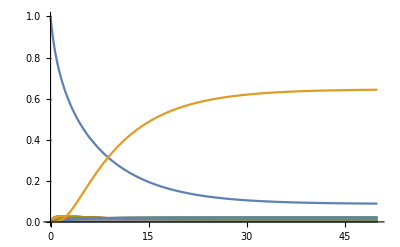

```mathematica
Tmax=50;
Plot[{solSpecialRes},{t,0,Tmax},PlotRange->{{0,Tmax},{0,1}}]
```

#### Find special solution equivalent to release after stall

```mathematica
relCond = Solve[Table[IC[[k]]==If[arrayMicrostates[[k]]==Nmax,1,0],{k,Length[IC]}],Table[c[k],{k,1,Length[IC]}]] // Chop
```

{{c[1]→0.000456236,c[2]→0,c[3]→0,c[4]→0,c[5]→0,c[6]→0,c[7]→0,c[8]→-0.00448638,c[9]→0,c[10]→0,c[11]→0,c[12]→0,c[13]→0.0048366,c[14]→0,c[15]→0,c[16]→-0.0103134,c[17]→0,c[18]→0,c[19]→0,c[20]→0,c[21]→0,c[22]→0,c[23]→0,c[24]→0,c[25]→-0.0418558,c[26]→0,c[27]→0,c[28]→0,c[29]→0,c[30]→-0.13974,c[31]→0.234388,c[32]→0.654733}}

```mathematica
solSpecialRel = solOri/.relCond//Flatten;
```

```mathematica
Sum[solSpecialRel[[k]],{k,1,Length[solSpecialRel]}]/.t->100
```

1.

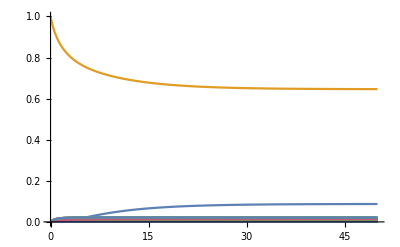

```mathematica
Tmax=50;
Plot[{solSpecialRel},{t,0,Tmax},PlotRange->{{0,Tmax},{0,1}}]
```

### Stationary solution

```mathematica
solSpecialRes/. t-> 100000//MatrixForm;
```

General::munfl: Exp[-500000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-353881.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-309570.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
mRes[t_]:= Sum[solSpecialRes[[k]]*arrayMicrostates[[k]],{k,1,Length[solSpecialRes]}]
sdRes[t_]:=Sqrt[Sum[solSpecialRes[[k]]*arrayMicrostates[[k]]^2,{k,1,Length[solSpecialRes]}]-mRes[t]^2]
```

```mathematica
mRel[t_]:= Sum[solSpecialRel[[k]]*arrayMicrostates[[k]],{k,1,Length[solSpecialRel]}]
sdRel[t_]:=Sqrt[Sum[solSpecialRel[[k]]*arrayMicrostates[[k]]^2,{k,1,Length[solSpecialRel]}]-mRel[t]^2]
```

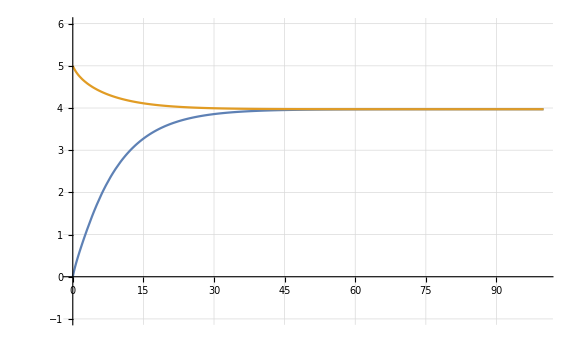

```mathematica
Tmax=100;
plot=Show[Plot[{mRes[t],mRel[t]},{t,0,Tmax},PlotRange->{{0,Tmax},{-1,Nmax+1}},GridLines->Automatic, TargetUnits->"Minutes"],ImageSize->Large]
```